```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
Jamdataupline={{0.007960288219017161,0.021975308641975312},
{0.008487749811991623,0.02246913580246914},
{0.009114908681193929,0.023209876543209884},
{0.00971887729646511,0.02395061728395062},
{0.010399868879138529,0.024691358024691357},
{0.01104952612960076,0.0254320987654321},
{0.011697995638610362,0.02617283950617284},3
{0.012384522228003592,0.02691358024691358},
{0.013299613168261061,0.027654320987654323},
{0.014384498882876644,0.02864197530864198},
{0.015447367870918828,0.02950617283950617},
{0.016470935490617823,0.030370370370370367},
{0.017687971042538296,0.03123456790123457},
{0.019130827076154256,0.03222222222222222},
{0.020691380811147922,0.03333333333333333},
{0.022379233169986138,0.034320987654320984},
{0.024377934398955595,0.035432098765432095},
{0.02617921720179419,0.0362962962962963},
{0.02831472734052692,0.03728395061728395},
{0.030406899326506996,0.0382716049382716},
{0.03288727302518013,0.03925925925925926},
{0.035317309892251736,0.04},
{0.037926901907322536,0.04098765432098766},
{0.04043999986888007,0.041728395061728395},
{0.043428106864267235,0.04246913580246914},
{0.04747561378997425,0.04333333333333333},
{0.05080218046913025,0.04395061728395062},
{0.05533935025357831,0.044691358024691354},
{0.06028173708703507,0.0454320987654321},
{0.0651990827714951,0.045802469135802465},
{0.06951927961775613,0.04617283950617284},
{0.07359919513555008,0.046419753086419754},
{0.07847599703514618,0.04666666666666666},
{0.08427457953937503,0.04679012345679012},
{0.09114908681193928,0.04679012345679012},
{0.09999999999999998,0.04647540983606556},
{0.11294964028776977,0.045983606557377044},
{0.12589928057553956,0.04524590163934425},
{0.1417266187050359,0.044385245901639336},
{0.15755395683453233,0.043401639344262284},
{0.17194244604316544,0.04254098360655737},
{0.19064748201438841,0.041311475409836054},
{0.20503597122302153,0.04057377049180327},
{0.2208633093525173,0.039713114754098354},
{0.23597122302158258,0.03860655737704917},
{0.24676258992805755,0.03749999999999999},
{0.25971223021582734,0.03614754098360655},
{0.2712230215827337,0.0347950819672131},
{0.2827338129496402,0.03331967213114753},
{0.29424460431654675,0.031721311475409825},
{0.30719424460431644,0.029999999999999992},
{0.3187050359712231,0.02815573770491802},
{0.3323741007194243,0.026065573770491797},
{0.3446043165467627,0.024098360655737693},
{0.35683453237410057,0.02237704918032786},
{0.36906474820143875,0.020409836065573762},
{0.38201438848920855,0.018688524590163923},
{0.39712230215827393,0.016967213114754097},
{0.4107913669064748,0.015245901639344257},
{0.42446043165467606,0.014016393442622947},
{0.4374100719424462,0.013032786885245895},
{0.45107913669064736,0.01204918032786885},
{0.4683453237410068,0.011188524590163923},
{0.48273381294964013,0.010573770491803275},
{0.49856115107913657,0.010081967213114745}};
```

```mathematica
Jamdatadownline={{0.007960288219017161,0.0064197530864197605},
{0.00867122579786319,0.006913580246913589},
{0.00951323386898418,0.007407407407407404},
{0.010289254298577423,0.007901234567901233},
{0.011450475699382831,0.008395061728395062},
{0.012562359207182957,0.00888888888888889},
{0.013782210712765435,0.009259259259259259},
{0.014906463225145543,0.00962962962962964},
{0.0161224240808339,0.010123456790123456},
{0.017313708164284434,0.010617283950617284},
{0.018726034554294106,0.010987654320987666},
{0.02054440171510448,0.011481481481481495},
{0.022539339047347937,0.01197530864197531},
{0.024904901574760142,0.0125925925925926},
{0.027518736070544687,0.013333333333333329},
{0.0299764490398009,0.013827160493827158},
{0.032076867519409434,0.014320987654320994},
{0.03494166963508326,0.014938271604938276},
{0.03738999593658945,0.015432098765432098},
{0.0405844003166461,0.01604938271604938},
{0.043894980525463256,0.01666666666666667},
{0.04798600015558144,0.017283950617283952},
{0.05171568613326445,0.01802469135802469},
{0.055735259941711135,0.018641975308641985},
{0.059853531965982566,0.019259259259259268},
{0.06427610264219598,0.01975308641975309},
{0.06976751441344664,0.020493827160493833},
{0.07465605128970534,0.021111111111111115},
{0.07903743130153583,0.021481481481481483},
{0.08427457953937503,0.021975308641975312},
{0.09114908681193928,0.02271604938271605},{0.09999999999999998,0.023114754098360654},
{0.1086330935251798,0.023852459016393435},
{0.12014388489208627,0.024467213114754097},
{0.13309352517985606,0.024713114754098355},
{0.14316546762589932,0.024713114754098355},
{0.15899280575539565,0.024590163934426222},
{0.17338129496402876,0.024221311475409825},
{0.18633093525179845,0.023360655737704905},
{0.19856115107913652,0.02237704918032786},
{0.2086330935251799,0.021270491803278682},
{0.21870503597122315,0.01991803278688524},
{0.22805755395683458,0.018934426229508194},
{0.23812949640287762,0.017704918032786877},
{0.24820143884892076,0.016475409836065574},
{0.2575539568345323,0.015245901639344257},
{0.2705035971223022,0.01377049180327869},
{0.28129496402877685,0.012540983606557365},
{0.29280575539568343,0.01131147540983607},
{0.3057553956834531,0.00983606557377048},
{0.318705035971223,0.008360655737704906},
{0.33453237410071934,0.00663934426229508},
{0.34892086330935246,0.00491803278688524},
{0.36330935251798546,0.00368852459016393},
{0.37482014388489193,0.0025819672131147525},
{0.38920863309352505,0.0009836065573770453},
{0.4064748201438847,-0.0007377049180327944},
{0.4215827338129493,-0.0023360655737705016},
{0.4338129496402876,-0.00368852459016393},
{0.44244604316546754,-0.004672131147540989},
{0.4553956834532372,-0.006024590163934432},
{0.4683453237410071,-0.007377049180327874},
{0.4798561151079137,-0.008606557377049184},
{0.4971223021582736,-0.009959016393442627}
};
```

```mathematica
Jamdatauplinef=Interpolation[Jamdataupline];
Jamdatadownlinef=Interpolation[Jamdatadownline];
```

```mathematica
leftL1=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-krleft-xi0-L1.wdx"];
HdL1=Query[1,1]@leftL1;
HdnL1=Interpolation[Flatten[HdL1,1]];
HdfL1[x_,t_]=HdnL1[x,t];


rightL1=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-krright-xi0-L1.wdx"];
HeL1=Query[1,1]@rightL1;
HenL1=Interpolation[Flatten[HeL1,1]];
HefL1[x_,t_]=HenL1[x,t];
```

```mathematica
leftL08=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-krleft-xi0-L08.wdx"];
HdL08=Query[1,1]@leftL08;
HdnL08=Interpolation[Flatten[HdL08,1]];
HdfL08[x_,t_]=HdnL08[x,t];


rightL08=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-krright-xi0-L08.wdx"];
HeL08=Query[1,1]@rightL08;
HenL08=Interpolation[Flatten[HeL08,1]];
HefL08[x_,t_]=HenL08[x,t];
leftL09=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-krleft-xi0-L09.wdx"];
HdL09=Query[1,1]@leftL09;
HdnL09=Interpolation[Flatten[HdL09,1]];
HdfL09[x_,t_]=HdnL09[x,t];


rightL09=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-krright-xi0-L09.wdx"];
HeL09=Query[1,1]@rightL09;
HenL09=Interpolation[Flatten[HeL09,1]];
HefL09[x_,t_]=HenL09[x,t];


leftL11=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-krleft-xi0-L11.wdx"];
HdL11=Query[1,1]@leftL11;
HdnL11=Interpolation[Flatten[HdL11,1]];
HdfL11[x_,t_]=HdnL11[x,t];


rightL11=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-krright-xi0-L11.wdx"];
HeL11=Query[1,1]@rightL11;
HenL11=Interpolation[Flatten[HeL11,1]];
HefL11[x_,t_]=HenL11[x,t];


leftL12=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-krleft-xi0-L12.wdx"];
HdL12=Query[1,1]@leftL12;
HdnL12=Interpolation[Flatten[HdL12,1]];
HdfL12[x_,t_]=HdnL12[x,t];


rightL12=Import["G:\\calc-online\\polarized\\juanji\\result\\convolution-rbw-krright-xi0-L12.wdx"];
HeL12=Query[1,1]@rightL12;
HenL12=Interpolation[Flatten[HeL12,1]];
HefL12[x_,t_]=HenL12[x,t];
```

```mathematica
np1coe=((-I)/((2π)^4*2*fc^2))*(Dc+Fc)/2;
```

```mathematica
xudL1[x_,t_]:=-np1coe*(HdfL1[x, t] + HefL1[x, t]);
```

InterpolatingFunction::dmval: Input value {0.0000204286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

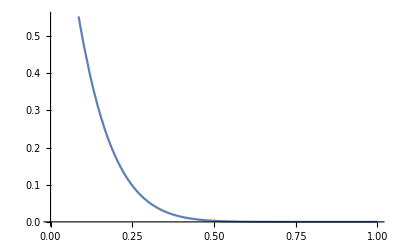

```mathematica
Plot[xudL1[x,0],{x,0,1}]
```

```mathematica
xudL08[x_,t_]:=-np1coe*(HdfL08[x, t] + HefL08[x, t]);
xudL09[x_,t_]:=-np1coe*(HdfL09[x, t] + HefL09[x, t]);
xudL11[x_,t_]:=-np1coe*(HdfL11[x, t] + HefL11[x, t]);
xudL12[x_,t_]:=-np1coe*(HdfL12[x, t] + HefL12[x, t]);
```

InterpolatingFunction::dmval: Input value {0.0000102143,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

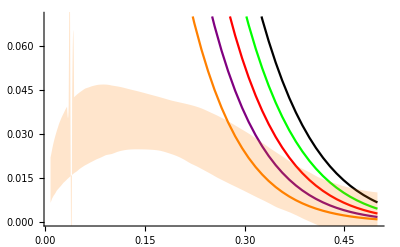

```mathematica
Show[Plot[xudL1[x,0],{x,0,0.5},PlotRange->{All,{0,0.07}},PlotStyle->Red],Plot[xudL11[x,0],{x,0,0.5},PlotRange->{All,{0,0.07}},PlotStyle->Green],Plot[xudL12[x,0],{x,0,0.5},PlotRange->{All,{0,0.07}},PlotStyle->Black],Plot[xudL08[x,0],{x,0,0.5},PlotRange->{All,{0,0.07}},PlotStyle->Orange],Plot[xudL09[x,0],{x,0,0.5},PlotRange->{All,{0,0.07}},PlotStyle->Purple],Plot[{Jamdatauplinef[x],Jamdatadownlinef[x]},{x,0.008,0.5},PlotStyle->Directive[Orange,Opacity[0]], Filling -> {1 -> {2}}]]
```

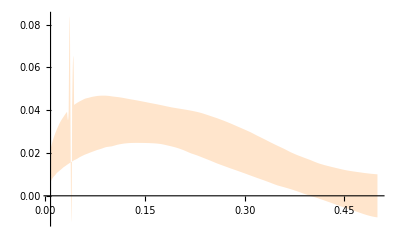

```mathematica
Plot[{Jamdatauplinef[x],Jamdatadownlinef[x]},{x,0.008,0.5},PlotStyle->Directive[Orange,Opacity[0]], Filling -> {1 -> {2}}]
```

```mathematica
Jamdatauplinef[0.008]
```

0.0220062

```mathematica
Jamdatadownlinef[x]
```

InterpolatingFunction[…][x]

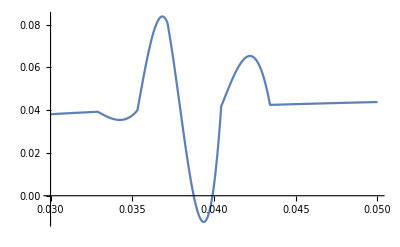

```mathematica
Plot[Jamdatauplinef[x],{x,0.03,0.05}]
```

```mathematica
NIntegrate[xudL1[x,0],{x,0.01,1}]
```

0.115304